Data Import

```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210421_OR_model_and_other_lines_sliding"];
```

```mathematica
Get["../algoritm_packages/SingleNetworks-algorithm-package.wl"]
(* ?SingleNetworks`* *)
```

```mathematica
datafull=Import["../data/cgl_manipulated_31230.csv"];
```

Data with Sliding Time Windows

```mathematica
x1=Round@Ceiling[Length@datafull/7,1];
{a,b,c,d,e,f,g}=Join[Range[x1,Length@datafull,x1],{Length@datafull}];
data1=Join[{Take[datafull,{1,a}]},Flatten[Table[{Take[datafull,{z[[1]]-x1/2,z[[2]]-x1/2}],Take[datafull,{z[[1]],z[[2]]}]},{z,
Partition[{a,b,c,d,e,f,g},2,1]}],1]];
win1=Length@data1;
```

```mathematica
x2=Round@Ceiling[Length@datafull/11,1];
{a,b,c,d,e,f,g,h,i,j,k}=Join[Range[x2,Length@datafull,x2],{Length@datafull}];
data2=Join[{Take[datafull,{1,a}]},Flatten[Table[{Take[datafull,{z[[1]]-x2/2,z[[2]]-x2/2}],Take[datafull,{z[[1]],z[[2]]}]},{z,
Partition[{a,b,c,d,e,f,g,h,i,j,k},2,1]}],1]];
win2=Length@data2;
```

Investigation of Constraints Impact in Time Windows

Fixed Step Size Networks

Width Feature

```mathematica
step1=11;
step2=11;
```

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedstep1=snetworkdatabinnedintimewindows[data1,9,step1,win1];]
```

{7.94811,Null}

```mathematica
graphsandnodenumbers1=Table[snetworkgraph[widthdataintimewindowsFixedstep1[[1]][[i]],widthdataintimewindowsFixedstep1[[2]][[i]],2,7,400,Green],{i,Range@win1}];
modularityvalues1=Table[N@GraphAssortativity[graphsandnodenumbers1[[i]][[1]],FindGraphCommunities[graphsandnodenumbers1[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers1}];
```

```mathematica
singlerandomgraphserdren1=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers1[[All,1]]}];
singlerandomerdrenmodularityvalues1=Table[N@GraphAssortativity[singlerandomgraphserdren1[[i]],FindGraphCommunities[singlerandomgraphserdren1[[i]]],"Normalized"->False],{i,Length@singlerandomgraphserdren1}];
singlerandomgraphscomm1=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers1[[All,1]]}];
singlerandomcommmodularityvalues1=Table[N@GraphAssortativity[singlerandomgraphscomm1[[i]],FindGraphCommunities[singlerandomgraphscomm1[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm1}];
```

```mathematica
AbsoluteTiming[Zscoresmodularity1=Table[randomnessfunctionformodularitytwonullmodel[i],{i,graphsandnodenumbers1[[All,1]]}];]
```

{418.19,Null}

```mathematica
bucketnode11=Round@N@Mean@graphsandnodenumbers1[[All,2]]
```

71

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedstep2=snetworkdatabinnedintimewindows[data2,9,step2,win2];]
```

{15.2616,Null}

```mathematica
graphsandnodenumbers12=Table[snetworkgraph[widthdataintimewindowsFixedstep2[[1]][[i]],widthdataintimewindowsFixedstep2[[2]][[i]],2,7,400,Green],{i,Range@win2}];
modularityvalues12=Table[N@GraphAssortativity[graphsandnodenumbers12[[i]][[1]],FindGraphCommunities[graphsandnodenumbers12[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers12}];
```

```mathematica
bucketnode12=Round@N@Mean@graphsandnodenumbers12[[All,2]]
```

66

```mathematica
(* AbsoluteTiming[widthdatafullFixedstep1=snetworkdatabinned[9,step1,datafull];
graphsandnodenumbersdatafull1=snetworkgraph[widthdatafullFixedstep1[[1]],widthdatafullFixedstep1[[2]],2,7,400,Green];]
randomnessvalues1=randomnessvaluesformodularitytwonullmodel[graphsandnodenumbersdatafull1[[1]]];*)
```

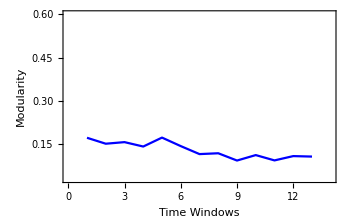
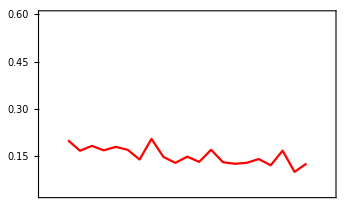
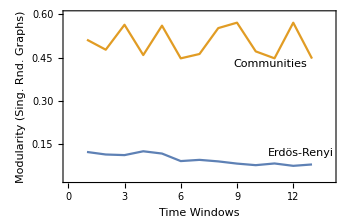
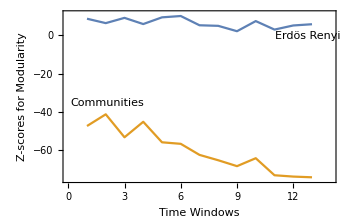

```mathematica
modularityplotrange={0.03,0.6};(*MinMax[{modularityvalues1,singlerandomcommmodularityvalues1,singlerandomerdrenmodularityvalues1,modularityvalues12}]*)
{Overlay[{ListLinePlot[Thread[{Range@win1,modularityvalues1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},modularityplotrange}],ListLinePlot[Thread[{Range@win2,modularityvalues12}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},modularityplotrange}]}],
ListLinePlot[{Thread[{Range@win1,singlerandomerdrenmodularityvalues1}],Thread[{Range@win1,singlerandomcommmodularityvalues1}]},Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{Style["Time Windows",Blue],None}},ImageSize->350,PlotRange->{{0,win1+1},modularityplotrange},PlotLabels->Placed[{"Erdös-Renyi","Communities"},{Scaled[1],Below}]],
ListLinePlot[{Thread[{Range@win1,Zscoresmodularity1[[All,1]]}],Thread[{Range@win1,Zscoresmodularity1[[All,2]]}]},Frame->True,ImagePadding->42,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-scores for Modularity",None},{Style["Time Windows",Blue],None}},ImageSize->350,PlotRange->{{0,win1+1},MinMax[Flatten[Zscoresmodularity1],1]},PlotLabels->Placed[{"Erdös Renyi","Communities"},{Scaled[1],Above}]]}
```

Thickness Feature

```mathematica
step1=0.05;
step2=0.05;
```

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedstep1=snetworkdatabinnedintimewindows[data1,10,step1,win1];]
```

{8.95846,Null}

```mathematica
graphsandnodenumbers2=Table[snetworkgraph[thicknessdataintimewindowsFixedstep1[[1]][[i]],thicknessdataintimewindowsFixedstep1[[2]][[i]],2,7,400,RGBColor[0.1,0.5,1.]],{i,Range@win1}];
modularityvalues2=Table[N@GraphAssortativity[graphsandnodenumbers2[[i]][[1]],FindGraphCommunities[graphsandnodenumbers2[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers2}];
```

```mathematica
singlerandomgraphserdren2=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers2[[All,1]]}];
singlerandomerdrenmodularityvalues2=Table[N@GraphAssortativity[singlerandomgraphserdren2[[i]],FindGraphCommunities[singlerandomgraphserdren2[[i]]],"Normalized"->False],{i,Length@singlerandomgraphserdren2}];
singlerandomgraphscomm2=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers2[[All,1]]}];
singlerandomcommmodularityvalues2=Table[N@GraphAssortativity[singlerandomgraphscomm2[[i]],FindGraphCommunities[singlerandomgraphscomm2[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm2}];
```

```mathematica
AbsoluteTiming[Zscoresmodularity2=Table[randomnessfunctionformodularitytwonullmodel[i],{i,graphsandnodenumbers2[[All,1]]}];]
```

{173.937,Null}

```mathematica
bucketnode21=Round@N@Mean@graphsandnodenumbers2[[All,2]]
```

50

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedstep2=snetworkdatabinnedintimewindows[data2,10,step1,win2];]
```

{4.65338,Null}

```mathematica
graphsandnodenumbers22=Table[snetworkgraph[thicknessdataintimewindowsFixedstep2[[1]][[i]],thicknessdataintimewindowsFixedstep2[[2]][[i]],2,7,400,RGBColor[0.1,0.5,1.]],{i,Range@win2}];
modularityvalues22=Table[N@GraphAssortativity[graphsandnodenumbers22[[i]][[1]],FindGraphCommunities[graphsandnodenumbers22[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers22}];
```

```mathematica
bucketnode22=Round@N@Mean@graphsandnodenumbers22[[All,2]]
```

47

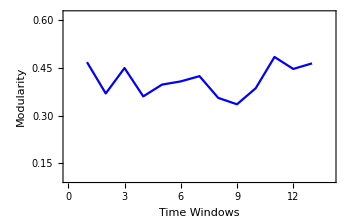
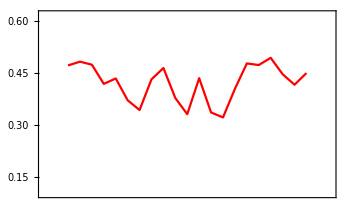
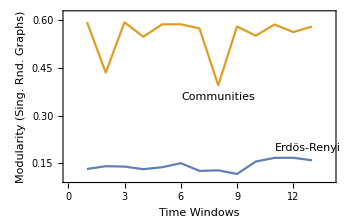
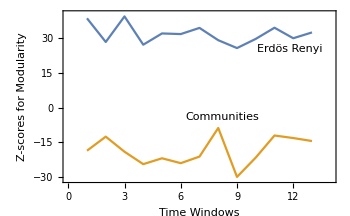

```mathematica
modularityplotrange={0.1,0.62};(* MinMax[{modularityvalues2,singlerandomcommmodularityvalues2,singlerandomerdrenmodularityvalues2,modularityvalues22}];*)
{Overlay[{ListLinePlot[Thread[{Range@win1,modularityvalues2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},modularityplotrange}],ListLinePlot[Thread[{Range@win2,modularityvalues22}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},modularityplotrange}]}],
ListLinePlot[{Thread[{Range@win1,singlerandomerdrenmodularityvalues2}],Thread[{Range@win1,singlerandomcommmodularityvalues2}]},Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{Style["Time Windows",Blue],None}},ImageSize->350,PlotRange->{{0,win1+1},modularityplotrange},PlotLabels->Placed[{"Erdös-Renyi","Communities"},{Scaled[1],Below}]],
ListLinePlot[{Thread[{Range@win1,Zscoresmodularity2[[All,1]]}],Thread[{Range@win1,Zscoresmodularity2[[All,2]]}]},Frame->True,ImagePadding->42,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-scores for Modularity",None},{Style["Time Windows",Blue],None}},ImageSize->350,PlotRange->{{0,win1+1},MinMax[Flatten[Zscoresmodularity2],1]},PlotLabels->Placed[{"Erdös Renyi","Communities"},{Scaled[1],Above}]]}
```

Fixed Bucket Size Networks

Width Feature

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedbucket1=snetworkdatafxdbucketintimewindows[data1,9,bucketnode11,win1];]
```

{0.987252,Null}

```mathematica
graphsandnodenumbers3=Table[snetworkgraph[widthdataintimewindowsFixedbucket1[[1]][[i]],widthdataintimewindowsFixedbucket1[[2]][[i]],1.5,7,400,Green],{i,Range@win1}];
modularityvalues3=Table[N@GraphAssortativity[graphsandnodenumbers3[[i]][[1]],FindGraphCommunities[graphsandnodenumbers3[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers3}];
```

```mathematica
singlerandomgraphserdren3=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers3[[All,1]]}];
singlerandomerdrenmodularityvalues3=Table[N@GraphAssortativity[singlerandomgraphserdren3[[i]],FindGraphCommunities[singlerandomgraphserdren3[[i]]],"Normalized"->False],{i,Length@singlerandomgraphserdren3}];
singlerandomgraphscomm3=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers3[[All,1]]}];
singlerandomcommmodularityvalues3=Table[N@GraphAssortativity[singlerandomgraphscomm3[[i]],FindGraphCommunities[singlerandomgraphscomm3[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm3}];
```

```mathematica
AbsoluteTiming[Zscoresmodularity3=Table[randomnessfunctionformodularitytwonullmodel[i],{i,graphsandnodenumbers3[[All,1]]}];]
```

{176.668,Null}

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedbucket2=snetworkdatafxdbucketintimewindows[data2,9,bucketnode12,win2];]
```

{1.06403,Null}

```mathematica
graphsandnodenumbers32=Table[snetworkgraph[widthdataintimewindowsFixedbucket2[[1]][[i]],widthdataintimewindowsFixedbucket2[[2]][[i]],1.5,7,400,Green],{i,Range@win2}];
modularityvalues32=Table[N@GraphAssortativity[graphsandnodenumbers32[[i]][[1]],FindGraphCommunities[graphsandnodenumbers32[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers32}];
```

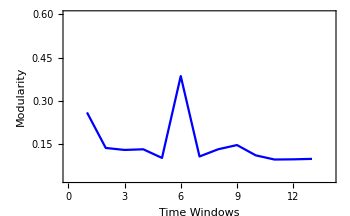
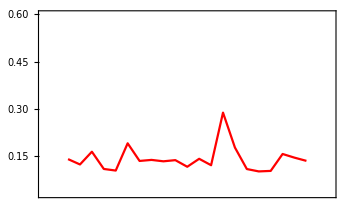
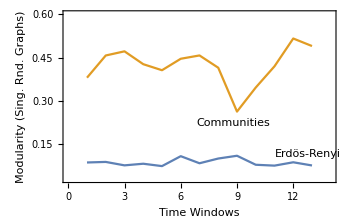
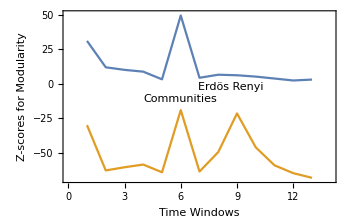

```mathematica
modularityplotrange={0.03,0.6};(* MinMax[{modularityvalues3,singlerandomcommmodularityvalues3,singlerandomerdrenmodularityvalues3,modularityvalues32}];*)
{Overlay[{ListLinePlot[Thread[{Range@win1,modularityvalues3}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},modularityplotrange}],ListLinePlot[Thread[{Range@win2,modularityvalues32}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},modularityplotrange}]}],
ListLinePlot[{Thread[{Range@win1,singlerandomerdrenmodularityvalues3}],Thread[{Range@win1,singlerandomcommmodularityvalues3}]},Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{Style["Time Windows",Blue],None}},ImageSize->350,PlotRange->{{0,win1+1},modularityplotrange},PlotLabels->Placed[{"Erdös-Renyi","Communities"},{Scaled[1],Below}]],
ListLinePlot[{Thread[{Range@win1,Zscoresmodularity3[[All,1]]}],Thread[{Range@win1,Zscoresmodularity3[[All,2]]}]},Frame->True,ImagePadding->42,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-scores for Modularity",None},{Style["Time Windows",Blue],None}},ImageSize->350,PlotRange->{{0,win1+1},MinMax[Flatten[Zscoresmodularity3],1]},PlotLabels->Placed[{"Erdös Renyi","Communities"},{Scaled[1],Above}]]}
```

Thickness Feature

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedbucket1=snetworkdatafxdbucketintimewindows[data1,10,bucketnode21,win1];]
```

{1.14092,Null}

```mathematica
graphsandnodenumbers4=Table[snetworkgraph[thicknessdataintimewindowsFixedbucket1[[1]][[i]],thicknessdataintimewindowsFixedbucket1[[2]][[i]],1.5,7,400,RGBColor[0.1,0.5,1.]],{i,Range@win1}];
modularityvalues4=Table[N@GraphAssortativity[graphsandnodenumbers4[[i]][[1]],FindGraphCommunities[graphsandnodenumbers4[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers4}];
```

```mathematica
singlerandomgraphserdren4=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers4[[All,1]]}];
singlerandomerdrenmodularityvalues4=Table[N@GraphAssortativity[singlerandomgraphserdren4[[i]],FindGraphCommunities[singlerandomgraphserdren4[[i]]],"Normalized"->False],{i,Length@singlerandomgraphserdren4}];
singlerandomgraphscomm4=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers4[[All,1]]}];
singlerandomcommmodularityvalues4=Table[N@GraphAssortativity[singlerandomgraphscomm4[[i]],FindGraphCommunities[singlerandomgraphscomm4[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm4}];
```

```mathematica
AbsoluteTiming[Zscoresmodularity4=Table[randomnessfunctionformodularitytwonullmodel[i],{i,graphsandnodenumbers4[[All,1]]}];]
```

{110.553,Null}

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedbucket2=snetworkdatafxdbucketintimewindows[data2,10,bucketnode22,win2];]
```

{1.11465,Null}

```mathematica
graphsandnodenumbers42=Table[snetworkgraph[thicknessdataintimewindowsFixedbucket2[[1]][[i]],thicknessdataintimewindowsFixedbucket2[[2]][[i]],1.5,7,400,RGBColor[0.1,0.5,1.]],{i,Range@win2}];
modularityvalues42=Table[N@GraphAssortativity[graphsandnodenumbers42[[i]][[1]],FindGraphCommunities[graphsandnodenumbers42[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers42}];
```

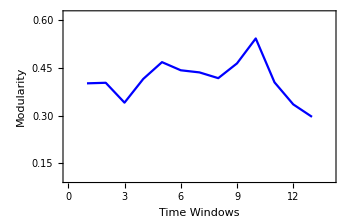
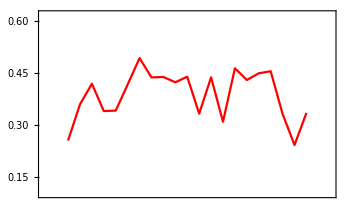
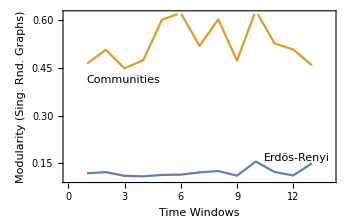
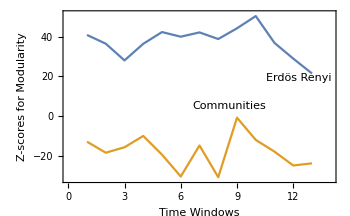

```mathematica
modularityplotrange={0.1,0.62};(* MinMax[{modularityvalues4,singlerandomcommmodularityvalues4,singlerandomerdrenmodularityvalues4,modularityvalues42}];*)
{Overlay[{ListLinePlot[Thread[{Range@win1,modularityvalues4}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},modularityplotrange}],ListLinePlot[Thread[{Range@win2,modularityvalues42}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},modularityplotrange}]}],
ListLinePlot[{Thread[{Range@win1,singlerandomerdrenmodularityvalues4}],Thread[{Range@win1,singlerandomcommmodularityvalues4}]},Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{Style["Time Windows",Blue],None}},ImageSize->350,PlotRange->{{0,win1+1},modularityplotrange},PlotLabels->Placed[{"Erdös-Renyi","Communities"},{Scaled[1],Below}]],
ListLinePlot[{Thread[{Range@win1,Zscoresmodularity4[[All,1]]}],Thread[{Range@win1,Zscoresmodularity4[[All,2]]}]},Frame->True,ImagePadding->42,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-scores for Modularity",None},{Style["Time Windows",Blue],None}},ImageSize->350,PlotRange->{{0,win1+1},MinMax[Flatten[Zscoresmodularity4],1]},PlotLabels->Placed[{"Erdös Renyi","Communities"},{Scaled[1],Above}]]}
```